Your Title Here

```mathematica
Manipulate[
Module[{ρ,g,SG,γ,H,h,L,sol,δx,δy,r0,th,y0,x0,col,δw},
ρ=1000;(*kg/m3*)
g=9.8;(*m/s/s*)
SG[1]=1;SG[2]=13.6;SG[3]=0.85;(*water, Hg, oil*)
γ[i_]:=SG[i]*ρ*g;

If[CS==1,ΔP=15];If[CS==2,θ=30°];

H=10;h[1]=8;
L[0]=20;L[1]=(H-h[1])*Csc[θ];(*cm*)

sol=Quiet@Flatten@Solve[133.32*ΔP==(γ[2]*l2*Sin[θ]+γ[3]*h3-γ[1]*h[1])/100∧L[0]==L[1]+l2+h3*Csc[θ],{l2,h3}];
L[2]=l2/.sol;h[3]=h3/.sol;h[2]=L[2]*Sin[θ];

δx=2;δy=10;r0=3;th=1.25;
y0[1]=H-h[1];x0[1]=y0[1]*Cot[θ];
y0[2]=h[2];x0[2]=L[2]*Cos[θ];
y0[3]=h[3];x0[3]=y0[3]*Cot[θ];

col[1]=Yellow;col[2]=Blue;col[3]=Green;

δw=1.75*th;

Rasterize@Graphics3D[{
{col[1],Tube[{{-δx,0,δy},{0,0,δy},{0,0,y0[1]}},th],Sphere[{-δx-r0,0,δy},r0]},
{col[2],Tube[{{0,0,y0[1]},{0,0,0},{x0[1]+x0[2],0,y0[1]+y0[2]}},th]},
{col[3],Tube[{{x0[1]+x0[2],0,y0[1]+y0[2]},{x0[1]+x0[2]+x0[3],0,y0[1]+y0[2]+y0[3]},{δx+x0[1]+x0[2]+x0[3],0,y0[1]+y0[2]+y0[3]}},th],Sphere[{δx+r0+x0[1]+x0[2]+x0[3],0,y0[1]+y0[2]+y0[3]},r0]},

If[label,{
Line[{{δw,-th,H},{δw,-th,y0[1]}}],Line[{{0.8*δw,-th,#},{1.2*δw,-th,#}}]&/@{H,y0[1]},
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{δw,0,H-h[1]/2}],

Line[{{x0[1]+x0[2],-th,y0[1]+y0[2]},{x0[1]+x0[2],-th,y0[1]+y0[2]+y0[3]}}],
Line[{{x0[1]+x0[2]-0.2*δw,-th,#+y0[1]+y0[2]},{x0[1]+x0[2]+0.2*δw,-th,#+y0[1]+y0[2]}}]&/@{0,y0[3]},
Text[Style[Subscript[Style["h",Italic],3],18,Background->White],{x0[1]+x0[2],-th,y0[1]+y0[2]+y0[3]/2}],

Text[Style[Subscript[Style["P",Italic],"A"],18],{-δx-r0,-th,δy}],
Text[Style[Subscript[Style["P",Italic],"B"],18],{δx+r0+x0[1]+x0[2]+x0[3],0,y0[1]+y0[2]+y0[3]}],

Line[{{0,0,-th},{2*δx,0,-th}}],
(*Inset[Graphics[{Circle[{0,0},0.5,{0,π/2}]},ImageSize->75,PlotRange->{{-0.5,0.5},{-0.5,0.5}}],{0,0,-th}],*)
Text[Style["θ",Italic,18],{2*δx,0,-th},{1,-1}],

Text[Style[Column[{Row@{
Subscript[Style["h",Italic],1]," = ",h[1]," cm",Spacer@15,
Subscript[Style["L",Italic],2]," = ",NumberForm[L[2],{3,1}]," cm",Spacer@15,
Subscript[Style["h",Italic],3]," = ",NumberForm[h[3],{3,1}]," cm"},
If[CS==1,
Row@{"Δ",Style["P",Italic]," = ",Subscript[Style["P",Italic],"A"]," - ",Subscript[Style["P",Italic],"B"]," = ",ΔP," mmHg"},
Row@{Style["θ",Italic]," = ",θ}]
},Center],18],{7,0,17}]
}]
},Boxed->False,ViewPoint->Front,ImageSize->{600,450},PlotRange->{{-(δx+2*r0),27},{-r0,r0},{-th,18}},PlotRangePadding->None]
],
Grid@{{
Control[{{label,True,"labels"},{True,False}}],
Control[{{CS,1,""},{1->" angle ",2->" pressure "},Setter}],
PaneSelector[{
1->Control[{{θ,30°,"angle"},20°,45°,1°,Appearance->"Labeled"}],
2->Control[{{ΔP,15,Row@Riffle[{"pressure change "," - "," (mmHg)"},Subscript[Style["P",Italic],#]&/@{"A","B"}]},0,55,5,Appearance->"Labeled"}]
},Dynamic@CS]
}}
]
```

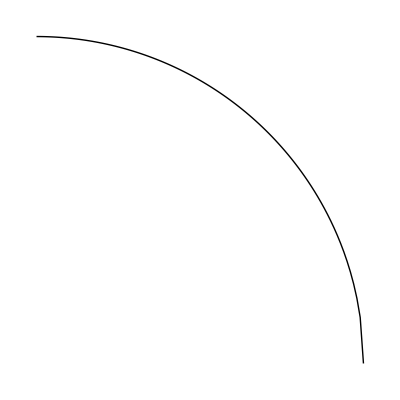

```mathematica
Graphics[{
(*Point[{#,√(1-#^2)}]&/@Range[0,1,0.1]*)
Line[{#,√(1-#^2)}&/@Range[0,1,0.01]]
}]
```

```mathematica
Module[{r,x0,y0},
r=1;x0=0.5;y0=-0.25;
]
```





```mathematica
x^2+y^2=r^2
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX